```mathematica
vfnfast[A_,μ_,σ_,δ_,x_]:=A^2 Block[{g=(δ^5+σ^5+2.69296 σ^4 δ+2.42843 σ^3 δ^2+4.47163 σ^2 δ^3+0.07842 σ δ^4)^(1/5),eta},
eta=δ/g;
eta=eta*(1.36603 - 0.47719 eta+0.11116 eta^2);
eta/(E^((x - μ)^2/(2*g^2))*g*Sqrt[2*Pi]) + (1 - eta)/(g*Pi*(1 + (x - μ)^2/g^2))
]
```

## Check normalization

```mathematica
??vfnfast
```

Global`vfnfast

vfnfast[A_,μ_,σ_,δ_,x_]:=A^2 Block[{g=(δ^5+σ^5+2.69296 σ^4 δ+2.42843 σ^3 δ^2+4.47163 σ^2 δ^3+0.07842 σ δ^4)^(1/5),eta},eta=δ/g;eta=eta (1.36603-0.47719 eta+0.11116 eta^2);eta/(ⅇ^((x-μ)^2/(2 g^2)) g √(2 π))+(1-eta)/(g π (1+(x-μ)^2/g^2))]

Integral scales quadratically with A, so given values for A, the relative intensities are proportional to A^2.

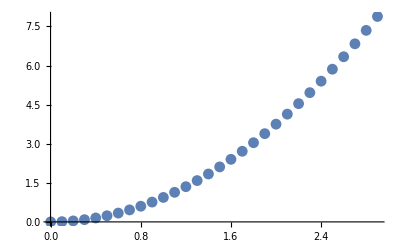

-Graphics-

```mathematica
ATable=Table[{A,NIntegrate[vfnfast[A,0,1,0,x],{x,-10,10}]},{A,0.001,3,0.1}];
ListPlot[ATable]
```

Integral is basically linearly dependent on σ, but relatively weakly. Slope does not depend on A.

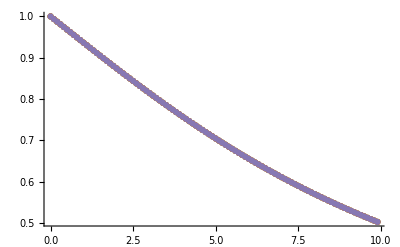

```mathematica
σTable=Table[{σ,NIntegrate[vfnfast[A,0,σ,0,x]/A^2,{x,-10,10}]},{A,0.1,2.1,0.5},{σ,0.001,10,0.1}];
ListPlot[σTable]
```

The slope does depend very slightly on δ. So the only two nontrivial variables are σ and δ. They vary very smoothly, so we can just make a lookup table for these.

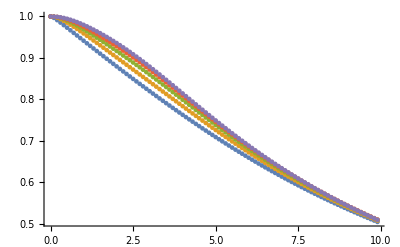

```mathematica
σTable=Table[{σ,NIntegrate[vfnfast[1,0,σ,δ,x],{x,-10,10}]},{δ,0.1,2.1,0.5},{σ,0.001,10,0.1}];
ListPlot[σTable]
```

For moderate values of δ, the integral does not depend on δ at all.

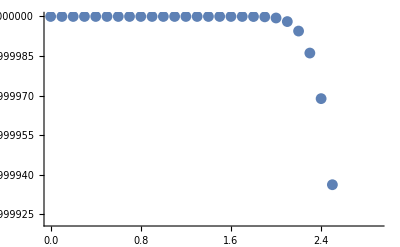

```mathematica
δTable=Table[{δ,NIntegrate[vfnfast[1,0,0,δ,x],{x,-10,10}]},{δ,0.001,3,0.1}];
ListPlot[δTable]
```

The integral also does not depend on μ.

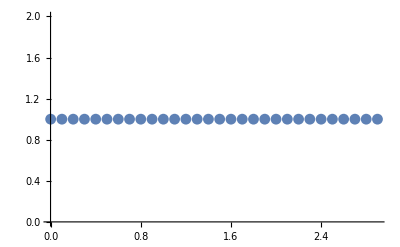

```mathematica
μTable=Table[{μ,NIntegrate[vfnfast[1,1,0,1,x],{x,-10,10}]},{μ,0.001,3,0.1}];
ListPlot[μTable]
```

This function computes a lookup table for the normalization of the fast voigt function:

```mathematica
vfnfastnormtable=Monitor[
Table[{{σ,δ},NIntegrate[vfnfast[1,0,σ,δ,x],{x,-15(δ+σ),+15(δ+σ)}]},{δ,0.001,10,0.01},{σ,0.001,10,0.01}]
,δ]
```

{{{{0.001,0.001},0.988999},{{0.011,0.001},0.963939},{{0.021,0.001},0.961103},{{0.031,0.001},0.960023},{{0.041,0.001},0.959454},991,{{9.961,0.001},0.957629},{{9.971,0.001},0.957629},{{9.981,0.001},0.957629},{{9.991,0.001},0.957629}},999}
 |  |  |  |

```mathematica
Flatten/@vfnfastnormtable
```

{{0.001,0.001,0.988999,0.011,0.001,0.963939,0.021,0.001,0.961103,0.031,0.001,0.960023,0.041,0.001,0.959454,2970,9.951,0.001,0.957629,9.961,0.001,0.957629,9.971,0.001,0.957629,9.981,0.001,0.957629,9.991,0.001,0.957629},998,{1}}
 |  |  |  |

```mathematica
ListPlot3D[vfnfastnormtable]
```

-Graphics3D-

```mathematica
vfnfastnorminterp=Interpolation[vfnfastnormtable]
```

Interpolation::indat: Data point {{{0.001, 0.001}, 0.988999}, {{0.011, 0.001}, 0.963939}, {{0.021, 0.001}, 0.961103}, {{0.031, 0.001}, 0.960023}, {{0.041, 0.001}, 0.959454}, « 41 », {{0.461, 0.001}, 0.957789}, {{0.471, 0.001}, 0.957785}, {{0.481, 0.001}, 0.957782}, {{0.491, 0.001}, 0.957779}, « 950 »} contains abscissa {{0.001, 0.001}, 0.988999}, which is not a real number.

Interpolation[{{{{0.001,0.001},0.988999},{{0.011,0.001},0.963939},{{0.021,0.001},0.961103},{{0.031,0.001},0.960023},992,{{9.961,0.001},0.957629},{{9.971,0.001},0.957629},{{9.981,0.001},0.957629},{{9.991,0.001},0.957629}},998,{1}}]
 |  |  |  |

```mathematica
Plot3D[vfnfastnorminterp[σ,δ],{σ,0.001,10},{δ,0.001,10}]
```

-Graphics3D-

Multiply by this function to generate the overall weight for A, μ, σ, δ. Divide by it to normalize a function:

```mathematica
vfnfastweight[A_,μ_,σ_,δ_]:=(A^2*vfnfastnorminterp[σ,δ])
```

```mathematica
DataPath="C:\\Users\\LukinLab\\Documents\\Ruffin\\Dropbox\\Harvard Physics\\Lukin Lab\\Scripts and Programs\\Transmission Spectra\\Clean Code\\VoigtNormalizationTable.csv"
```

C:\Users\LukinLab\Documents\Ruffin\Dropbox\Harvard Physics\Lukin Lab\Scripts and Programs\Transmission Spectra\Clean Code\VoigtNormalizationTable.csv

```mathematica
Export[DataPath,vfnfastnormtable];
```